# Synapse Models

## Steady-state Model

g_rise= g_sat-(g_sat-g_0)ⅇ^(-t_rise/τ_syn)
g_decay =g_rise ⅇ^((-(T-t_rise))/τ_syn)
g_ss=g_sat (ⅇ^(t_rise/τ_syn)-1)/(ⅇ^(T/τ_syn)-1)
(g^•)_syn=g_sat ⅇ^(-T/τ_syn) (ⅇ^(t_rise/τ_syn)-1)+g_syn(ⅇ^(-T/τ_syn)-1)

### Manipulator to understand theoretical behavior

```mathematica
gss[gsat_, T_, τsyn_, trise_]:=gsat (ⅇ^(trise/τsyn)-1)/(ⅇ^(T/τsyn)-1);
gdecay[grise0_,tdecay_,τsyn_]:=grise0 ⅇ^(-tdecay/τsyn);
grise[g0_,gsat_,trise_,τsyn_]:=gsat-(gsat-g0) ⅇ^(-trise/τsyn);
deltaG[gsyn_, gsat_,T_, trise_, τ_]:=gsat ⅇ^(-T/τ)(ⅇ^(trise/τ)-1)+gsyn(ⅇ^(-T/τ)-1);
meangk[gsat_, T_, trise_]:=gsat trise/T
DynamicModule[{gsat=4.0,Tinst = 2,trise=1,τsyn=1, plotXmax=5,plotYmin =0,plotYmax=4, g0inst,gdecay0},
g0inst:=Dynamic[gss[gsat, Tinst, τsyn, trise]];
gdecay0:=Dynamic[grise[g0inst,gsat,trise,τsyn]];
labelSize=15;
fieldSize=5;
titleLabelSize=16;
Panel[
Grid[{
{Grid[{{
Grid[{
{Style["g_sat",labelSize],Slider[Dynamic[gsat],{0.01,10}],InputField[Dynamic[gsat],FieldSize->fieldSize]},
{Style["τ_syn",labelSize],Slider[Dynamic[τsyn],{0.01,10}],InputField[Dynamic[τsyn],FieldSize->fieldSize]}
}],
Grid[{
{Style["T",labelSize],Slider[Dynamic[Tinst],{0.01,10}],InputField[Dynamic[Tinst],FieldSize->fieldSize]},
{Style["t_rise",labelSize],Slider[Dynamic[trise],{0,Dynamic[Tinst]}],InputField[Dynamic[trise],FieldSize->fieldSize]},
{Style["t_decay",labelSize],Panel[Dynamic[Tinst-trise],Background->LightGray]}
}]
}}]  },
{Grid[{
{
Grid[{{
Dynamic[Show[
Plot[
{
Piecewise[{{grise[gss[gsat, Tinst, τsyn, trise],gsat, t, τsyn],t<=trise},
{gdecay[grise[gss[gsat,Tinst,τsyn,trise],gsat, trise, τsyn],t-trise, τsyn],t>trise && t<Tinst }}],
grise[gss[gsat,Tinst,τsyn,trise],gsat, trise, τsyn],
meangk[gsat,Tinst,trise],
gdecay[grise[gss[gsat,Tinst,τsyn,trise],gsat, trise, τsyn],Tinst-trise, τsyn]
},
{t, 0,Tinst},
PlotRange->{plotYmin,plotYmax},
ImageSize->335,
PlotLabel->Style["Synapse conductance at steady state",titleLabelSize],AxesLabel->{Style["t",labelSize],Style["g_syn(g_0,g_sat,t_rise,τ_syn)",labelSize]},
PlotLegends->{"g_syn","g_decay0", "OverBar[g_kss]","g_0"},
PlotStyle->{Blue,Dashed,Dashed, Dashed}
]
]]
}}],
Grid[{
{Style["g_ss",labelSize],Panel[Dynamic[g0inst],Background->LightGray]},
{Style["g_decay_ss",labelSize],Panel[Dynamic[ grise[gss[gsat, Tinst, τsyn, trise],gsat, trise, τsyn]],Background->LightGray]},
{Style["(ḡ)_ss",labelSize],Panel[Dynamic[meangk[gsat, Tinst, trise]],Background->LightGray]},
{Style["x_max",labelSize],InputField[Dynamic[plotXmax],FieldSize->fieldSize]},
{Style["y_min",labelSize],InputField[Dynamic[plotYmin],FieldSize->fieldSize]},
{Style["y_max",labelSize],InputField[Dynamic[plotYmax],FieldSize->fieldSize]}
}]
}
} ] },
{Grid[{{
Dynamic[Show[
Plot[
{
gss[gsat, 1/f, τsyn, trise]
}, 
{f, 0,plotXmax},
PlotRange->{0,plotYmax},
ImageSize->335,
PlotLabel->Style["Steady-state conductance",titleLabelSize],
AxesLabel->{Style["f",labelSize],Style["g_syn",labelSize]}
],
ListPlot[{{1/Tinst, gss[gsat,Tinst,τsyn,trise]}},
PlotStyle->Red,
PlotMarkers->{"●",Medium}
]
]],
Dynamic[Show[
Plot[
{deltaG[gsyn,gsat, Tinst,trise, τsyn]},
{gsyn, 0,plotXmax},
ImageSize->335,
PlotLabel->Style["Phase portrait of synapse conductance",titleLabelSize],
AxesLabel->{Style["g_syn",labelSize],Style["Δg_syn",labelSize]}
],
ListPlot[{{ gss[gsat,Tinst,τsyn,trise],0}},
PlotStyle->Red,
PlotMarkers->{"●",Medium}]
]]
}}]}
}]
]
]
```

### Soma Model w/o Synapse

```mathematica
τ v'[t]==-v[t]+(v[t])^2/2+vin
```

τ v'(t)==(v(t))^2/2-v(t)+vin

#### Solved version of v(t)

```mathematica
solvt=DSolve[τ v'[t]==-v[t]+(v[t])^2/2+vin, v[t], t]
```

{{v(t)→√(2 vin-1) tan(1/2 (2 c_1 √(2 vin-1)+(t √(2 vin-1))/τ))+1}}

#### Solving for Firing Rate

```mathematica
τ∫ ⅆv/(-v+(v)^2/2+vin)
FullSimplify[(%/.v->∞)-(%/.v->0)]
```

(2 τ tan^-1((v-1)/(√(2 vin-1))))/(√(2 vin-1))

(2 τ (tan^-1(∞/(√(2 vin-1)))+cot^-1(√(2 vin-1))))/(√(2 vin-1))

Note: tan^-1(∞/(√(2 vin-1))) ⇒ π/2 b/c that is the value of x where tan(x) approaches ∞. ∴ h(v_in) =(π+2cot^-1(√(2 vin-1)))/(√(2 vin-1))

### Soma Model w/ Synapse

```mathematica
τ v'[t]==-v[t](1+gsyn)+(v[t])^2/2+vin+ gsyn erev
```

τ v'(t)==erev gsyn-(gsyn+1) v(t)+(v(t))^2/2+vin

#### Calculation of h(v_in, g_syn, e_rev)

```mathematica
∫ⅆv/(-v(1+gsyn)  +v^2/2+vin+gsyn erev)
FullSimplify[(%/.v->∞) -( %/.v->0)]
```

(2 tan^-1((-gsyn+v-1)/(√(2 erev gsyn-gsyn^2-2 gsyn+2 vin-1))))/(√(2 erev gsyn-gsyn^2-2 gsyn+2 vin-1))

(2 (tan^-1(∞/(√(gsyn (2 erev-gsyn-2)+2 vin-1)))+tan^-1((gsyn+1)/(√(gsyn (2 erev-gsyn-2)+2 vin-1)))))/(√(gsyn (2 erev-gsyn-2)+2 vin-1))

Note: tan^-1(∞/(√(2 (v_in+g_syn e_rev)-(1+g_syn)^2))) ⇒ π/2 b/c that is the value of x where tan(x) approaches ∞. ∴ h(v_in, g_syn) =(π+2tan^-1((1+g_syn)/(√(2 (v_in+g_syn e_rev)-(1+g_syn)^2))))/(√(2 (v_in+g_syn e_rev)-(1+g_syn)^2))

```mathematica
hsyn[vin_,gsyn_,erev_]:=(π+2 ArcTan[(1+gsyn)/(√(2 (vin+gsyn erev)-(1+gsyn)^2))])/(√(2 (vin+gsyn erev)-(1+gsyn)^2))
fsyn[vin_,gsyn_,erev_,τ_,tref_]:=1/(τ hsyn[vin,gsyn,erev]+tref)
```

#### Approximate Calculation of h(v_in, g_syn, e_rev) using Taylor Series

```mathematica
FullSimplify[Series[1/(hsyn[vin,g,e]/g),{vin,∞,0}]]
```

(√2 g √vin)/π-(2 (g (g+1)))/π^2+(√(1/vin) (8 g (g+1)^2-π^2 g (g (-2 e+g+2)+1)))/(2 √2 π^3)+O((1/vin)^1)

#### Plot theoretical firing rate with known v_in,t_ref, τ_m, g_syn, and e_rev

```mathematica
hsyn[vin_,gsyn_,erev_]:=(π+2 ArcTan[(1+gsyn)/(√(2 (vin+gsyn erev)-(1+gsyn)^2))])/(√(2 (vin+gsyn erev)-(1+gsyn)^2))
fsyn[vin_,gsyn_,erev_,τ_,tref_]:=1/(τ hsyn[vin,gsyn,erev]+tref)
Vin[Ic_,Il_,pqua_]:=pqua(Ic/Il)^2
Τ[Il_,ptau_]:=ptau/Il
Tref[Iref_,pref_]:=pref/Iref
Gsat[Igsat_,Il_,c1pgsat_]:=Igsat/(c1pgsat Il)
Erev[Ierev_,Il_,c1perev_]:=Ierev/(c1perev Il)
Gsyn[gsat_,trise_,ISI_]:=gsat trise/ISI 
Imprime[im_,vin_,τ_,gsyn_,erev_] :=(1/2 im^2-im + vin+gsyn(erev-im))/τ
ImprimeMin[vin_,τ_,gsyn_,erev_]:=(gsyn erev +vin-1/2(1+gsyn)^2)/τ
IgsatFn[c1pgsat_,c1perev_, Il_, Ierev_]:=c1pgsat/c1perev Ierev-c1pgsat Il+√(c1pgsat/c1perev Ierev(c1pgsat/c1perev Ierev-2 c1pgsat Il))
IerevFn[c1pgsat_,c1perev_,Il_,Igsat_]:=c1perev Il + 1/2 c1perev c1pgsat Il^2/Igsat+1/2 c1perev/c1pgsat Igsat
IgsatFn2[c1pgsat_,c2pgsat_, Il_]:=c2pgsat-c1pgsat Il+√(c2pgsat(c2pgsat-2 c1pgsat Il))
IerevFn2[c1perev_,c2perev_,Il_]:=c1perev Il + 1/2(c1perev Il)^2/c2perev+1/2 c2perev

TabView[{
Theoretical->DynamicModule[{vin=0.7,τ=.015,tref=.001,gsyn =0.5,erev = 2.0,vinMax=2, gsynMax = 5,fMax=20,vmMax=5,vprimeMax=100},
labelSize=12;
titleLabelSize=14;
 Panel[
Grid[{
{Grid[{
{Style["v_in",labelSize],Slider[Dynamic[vin],{0.0,20.0, .1}],InputField[Dynamic[vin],FieldSize->5]},
{Style["τ_m",labelSize],Slider[Dynamic[τ],{0.001,0.05,0.001}],InputField[Dynamic[τ],FieldSize->5]},
{Style["t_ref",labelSize],Slider[Dynamic[tref],{0.001,0.004, 0.001}],InputField[Dynamic[tref],FieldSize->5]},
{Style["v_m_max",labelSize],Slider[Dynamic[vmMax],{0.01,10, 0.5}],InputField[Dynamic[vmMax],FieldSize->5]},
{Style["v'_max",labelSize],Slider[Dynamic[vprimeMax],{5,300, 0.5}],InputField[Dynamic[vprimeMax],FieldSize->5]}
}],
Grid[{
{Style["g_syn",labelSize],Slider[Dynamic[gsyn],{0.0,10, 0.1}],InputField[Dynamic[gsyn],FieldSize->5]},
{Style["e_rev",labelSize],Slider[Dynamic[erev],{0.0,10, 0.1}],InputField[Dynamic[erev],FieldSize->5]},
{Style["g_syn_max",labelSize],Slider[Dynamic[gsynMax],{0.01,20, 0.5}],InputField[Dynamic[gsynMax],FieldSize->5]}
},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}
],
Grid[{
{Style["f(v_in)",labelSize],Panel[Dynamic[fsyn[vin,gsyn,erev,τ,tref]],Background->LightGray]},
{Style["v_in_max",labelSize],Slider[Dynamic[vinMax],{0.01,10, 0.5}],InputField[Dynamic[vinMax],FieldSize->5]},
{Style["f_max",labelSize],Slider[Dynamic[fMax],{5,100, 0.5}],InputField[Dynamic[fMax],FieldSize->5]}
},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}
]},
{Grid[{
{
Dynamic[
Plot[{Imprime[vm,vin,τ,gsyn,erev],Imprime[1+gsyn,vin,τ,gsyn,erev],ImprimeMin[vin,τ,vm-1,erev]},
{vm,0,vmMax},
PlotRange->{-5,vprimeMax},PlotLabel->Style["Quadratic Neuron w/ Synapse Phase Diagram",titleLabelSize],AxesLabel->{Style["v_m",labelSize],Style["v̇",labelSize]},PlotStyle->{Blue,Dashed,Dashed},
ImageSize->400]
]
}
}],
Grid[{
{
Dynamic[Show[
Plot[{fsyn[vin,gsynit,erev,τ,tref],fsyn[vin,gsyn,erev ,τ,tref]},{gsynit,0,gsynMax},PlotRange->{0,Max[fMax,fsyn[vin,gsynMax/2,erev ,τ,tref]]},PlotLabel->Style["Quadratic Neuron Firing Rate w/ Synapse",titleLabelSize],AxesLabel->{Style["g_syn",labelSize],Style["f(g_syn)",labelSize]},ImageSize->400,PlotStyle->{Blue,Dashed}],
ListPlot[{{gsyn, fsyn[vin,gsyn,erev ,τ,tref]}},PlotStyle->Red,PlotMarkers->{"●",Small}]
]]
}
}],
Grid[{
{Dynamic[
Show[
Plot[{fsyn[x0,gsyn,erev ,τ,tref],fsyn[vin,gsyn,erev ,τ,tref]},{x0,0,vinMax},PlotRange->{0,Max[fMax,fsyn[vinMax,gsyn,erev ,τ,tref]]},
ImageSize->400,
PlotStyle->{Blue,Dashed},
PlotLabel->Style["Quadratic Neuron Firing Rate w/ Synapse",titleLabelSize],
AxesLabel->{Style["v_in",labelSize],Style["f(v_in)",labelSize]}
],
ListPlot[{{vin, fsyn[vin,gsyn,erev ,τ,tref]}},PlotStyle->Red,PlotMarkers->{"●",Small}]
]]}
},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}
]
}
}](*Grid*)
](*Panel*)
](*DynamicModule Theoretical*)
,
Applied->DynamicModule[{Ic=0,Il=.45,Iref=2622.4075624201,Igsat=1.00, Ierev=.5,pqua=2.5592298,ptau=0.000603,pref=0.0279499,c1pgsat=1.187627, c1perev=0.319319,c2pgsat=1.906463, c2perev=.257392,tsynrise=.175,ISIsyn=.175,vinMax=2, gsynMax = 12,fMax=400,vmMax=5,vprimeMax=100, ilMax=0.5},
labelSize=12;
titleLabelSize=14;
 Panel[
Grid[{
{Grid[{
{Style["i_c",labelSize],Slider[Dynamic[Ic],{0.,5}],InputField[Dynamic[Ic],FieldSize->5]},{Style["i_l",labelSize],Slider[Dynamic[Il],{0.01,1,0.005}],InputField[Dynamic[Il],FieldSize->5]},{Style["i_ref",labelSize],Slider[Dynamic[Iref],{0.01,3000}],InputField[Dynamic[Iref],FieldSize->5]},
{Style["ρ_qua",labelSize],Slider[Dynamic[pqua],{0.5,6}],InputField[Dynamic[pqua],FieldSize->5]},{Style["ρ_tau",labelSize],Slider[Dynamic[ptau],{0.0001,0.005}],InputField[Dynamic[ptau],FieldSize->5]},{Style["ρ_ref",labelSize],Slider[Dynamic[pref],{0.,0.2}],InputField[Dynamic[pref],FieldSize->5]},
{Style["v_m_max",labelSize],Slider[Dynamic[vmMax],{0.01,10, 0.5}],InputField[Dynamic[vmMax],FieldSize->5]},
{Style["v'_max",labelSize],Slider[Dynamic[vprimeMax],{5,300, 0.5}],InputField[Dynamic[vprimeMax],FieldSize->5]}
}],
Grid[{
{Style["i_gsat",labelSize],Slider[Dynamic[Igsat],{0.001,4}],InputField[Dynamic[Igsat],FieldSize->5]},
{Style["i_erev",labelSize],Slider[Dynamic[Ierev],{0.01,1}],InputField[Dynamic[Ierev],FieldSize->5]},
{Style["c1_ρ_gsat",labelSize],Slider[Dynamic[c1pgsat],{0.1,2}],InputField[Dynamic[c1pgsat],FieldSize->5]},
{Style["c1_ρ_erev",labelSize],Slider[Dynamic[c1perev],{0.1,2}],InputField[Dynamic[c1perev],FieldSize->5]},
{Style["t_syn_rise(s)",labelSize],Slider[Dynamic[tsynrise],{0.001,Dynamic[ISIsyn],0.001}],InputField[Dynamic[tsynrise],FieldSize->5]},
{Style["ISI_syn(s)",labelSize],Slider[Dynamic[ISIsyn],{0.001,1,0.001}],InputField[Dynamic[ISIsyn],FieldSize->5]},
{Style["g_syn_max",labelSize],Slider[Dynamic[gsynMax],{0.01,20, 0.5}],InputField[Dynamic[gsynMax],FieldSize->5]},
{Style["I_l_max",labelSize],Slider[Dynamic[ilMax],{0.01,5, 0.5}],InputField[Dynamic[ilMax],FieldSize->5]}
},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}
],
Grid[{
{Style["v_in",labelSize],Panel[Dynamic[Vin[Ic,Il,pqua]],Background->LightGray]},
{Style["τ_m",labelSize],Panel[Dynamic[Τ[Il,ptau]],Background->LightGray]},
{Style["t_ref",labelSize],Panel[Dynamic[Tref[Iref,pref]],Background->LightGray]},
{Style["g_syn",labelSize],Panel[Dynamic[Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn]],Background->LightGray]},
{Style["g_sat",labelSize],Panel[Dynamic[Gsat[Igsat,Il,c1pgsat]],Background->LightGray]},
{Style["e_rev",labelSize],Panel[Dynamic[Erev[Ierev,Il,c1perev]],Background->LightGray]},
{Style["f(g_syn)",labelSize],Panel[Dynamic[fsyn[Vin[Ic,Il,pqua],Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev],Τ[Il,ptau],Tref[Iref,pref]]],Background->LightGray]},
{Style["v_in_max",labelSize],Slider[Dynamic[vinMax],{0.01,10, 0.5}],InputField[Dynamic[vinMax],FieldSize->5]},
{Style["f_max",labelSize],Slider[Dynamic[fMax],{5,500, 0.5}],InputField[Dynamic[fMax],FieldSize->5]}
},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}
]},
{Grid[{
{
Dynamic[
Plot[{Imprime[vm,Vin[Ic,Il,pqua],Τ[Il,ptau],Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev]],Imprime[1+Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Vin[Ic,Il,pqua],Τ[Il,ptau],Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev]],ImprimeMin[Vin[Ic,Il,pqua],Τ[Il,ptau],vm-1,Erev[Ierev,Il,c1perev]]},
{vm,0,vmMax},
PlotRange->{-5,vprimeMax},PlotLabel->Style["Quadratic Neuron w/ Synapse Phase Diagram",titleLabelSize],AxesLabel->{Style["v_m",labelSize],Style["v̇",labelSize]},PlotStyle->{Blue,Dashed,Dashed},
ImageSize->400]
]
}
}],
Grid[{
{
Dynamic[Show[
Plot[{
fsyn[Vin[Ic,Il,pqua],gsynit,Erev[Ierev,Il,c1perev],Τ[Il,ptau],Tref[Iref,pref]],
(*fsyn[Vin[Ic,Il,pqua],gsynit,Erev[IerevFn2[c1perev,c2perev,Il],Il,c1perev],Τ[Il,ptau],Tref[Iref,pref]],
fsyn[Vin[Ic,Il,pqua],gsynit,Erev[IerevFn[c1pgsat,c1perev,Il,Igsat],Il,c1perev],Τ[Il,ptau],Tref[Iref,pref]],*)
fsyn[Vin[Ic,Il,pqua],Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]
},{gsynit,0,gsynMax},
PlotRange->{0,Max[fMax,fsyn[Vin[Ic,Il,pqua],gsynMax/2,Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]]},
PlotLabel->Style["Quadratic Neuron Firing Rate w/ Synapse",titleLabelSize],
AxesLabel->{Style["g_syn",labelSize],Style["f(g_syn)",labelSize]},
ImageSize->400,
PlotStyle->{Blue,Dashed}],
ListPlot[{
{Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn], fsyn[Vin[Ic,Il,pqua],Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]}},
PlotStyle->Red,
PlotMarkers->{"●",Small}]
]]
}
}],
Grid[{
{Dynamic[
Show[
Plot[{
fsyn[x0,Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]],
fsyn[Vin[Ic,Il,pqua],Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]
},{x0,0,vinMax},
PlotRange->{0,Max[fMax,fsyn[vinMax,Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]]},
ImageSize->400,
PlotStyle->{Blue,Dashed},
PlotLabel->Style["Quadratic Neuron Firing Rate w/ Synapse",titleLabelSize],
AxesLabel->{Style["v_in",labelSize],Style["f(v_in)",labelSize]}
],
ListPlot[{{Vin[Ic,Il,pqua], fsyn[Vin[Ic,Il,pqua],Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]}},PlotStyle->Red,PlotMarkers->{"●",Small}]
]]}
},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}
]
},
{Grid[{
{Dynamic[
Show[
Plot[{IerevFn[c1pgsat,c1perev, Ilk, Igsat],IerevFn2[c1perev,c2perev, Ilk]},
{Ilk,0,ilMax},
PlotLabel->Style["Bifurcation Plot for I_erev",titleLabelSize],
AxesLabel->{Style["I_l",labelSize],Style["I_erev",labelSize]},
PlotStyle->{Blue,Dashed},
PlotRange->{0,All},
ImageSize->400,
Filling->{1-> Top}
],
ListPlot[{
{Il, IerevFn[c1pgsat,c1perev,Il,Igsat]}
},
PlotStyle->Darker[Green],
PlotMarkers->{"●",Small},
Filling->Axis
]
]
]
}
}],(*Grid IerevFn Plot*)
Grid[{
{Dynamic[
Show[
Plot[{IgsatFn[c1pgsat,c1perev, Ilk, Ierev],IgsatFn2[c1pgsat,c2pgsat, Ilk]},
{Ilk,0,ilMax},
ImageSize->400,
PlotRange->{0,All},
PlotStyle->{Blue,Dashed},
PlotLabel->Style["Bifurcation Plot for I_gsat",titleLabelSize],
AxesLabel->{Style["I_l",labelSize],Style["I_gsat",labelSize]},
Filling->{1-> Axis}
],
ListPlot[{
{Il, IgsatFn[c1pgsat,c1perev,Il,Ierev]}
},
PlotStyle->Darker[Green],
PlotMarkers->{"●",Small},
Filling-> Axis
]
]]}
}
],(*Grid IgsatFn Plot*)
Grid[{
{Style["i_gsat",labelSize],Slider[Dynamic[Igsat],{0.001,4}],InputField[Dynamic[Igsat],FieldSize->5]},
{Style["i_erev",labelSize],Slider[Dynamic[Ierev],{0.01,1}],InputField[Dynamic[Ierev],FieldSize->5]},
{Style["c1_ρ_gsat",labelSize],Slider[Dynamic[c1pgsat],{0.1,2}],InputField[Dynamic[c1pgsat],FieldSize->5]},
{Style["c1_ρ_erev",labelSize],Slider[Dynamic[c1perev],{0.1,2}],InputField[Dynamic[c1perev],FieldSize->5]},
{Style["c2_ρ_gsat",labelSize],Slider[Dynamic[c2pgsat],{0.1,2}],InputField[Dynamic[c2pgsat],FieldSize->5]},
{Style["c2_ρ_erev",labelSize],Slider[Dynamic[c2perev],{0.1,2}],InputField[Dynamic[c2perev],FieldSize->5]}
}] (* Grid pgsat,perev sliders *)
},
{Grid[{
{Dynamic[
Show[
Plot3D[{IerevFn[c1pgsat,c1perev, Ilk, IgsatSweep]},
{Ilk,0,ilMax},{IgsatSweep,0.25,2},
PlotLabel->Style["3D Bifurcation Plot for I_erev",titleLabelSize],
AxesLabel->{Style["I_l",labelSize],Style["I_gsat",labelSize],Style["I_erev",labelSize]},
PlotStyle->{Blue,Dashed},
PlotRange->{0,All},
ImageSize->400(*,
Filling->{1-> Top}*)
],
ParametricPlot3D[
{Ilk, Igsat,IerevFn[c1pgsat,c1perev,Ilk,Igsat]},
{Ilk,0,ilMax},
PlotStyle->{Directive[Red,Thick]}
](*,
ListPlot3D[{
{Il, Igsat,IerevFn[c1pgsat,c1perev,Il,Igsat]}
},
PlotStyle->Darker[Green],
Filling->Axis
]*)
]
]
}
}],(*Grid 3D Ierev[Igsat,Il] Plot*)
Grid[{
{Dynamic[
Show[
Plot3D[{IgsatFn[c1pgsat,c1perev, Ilk, IerevSweep]},
{Ilk,0,ilMax},{IerevSweep,0,1},
ImageSize->400,
PlotRange->{0,All},
PlotStyle->{Blue},
PlotLabel->Style["3D Bifurcation Plot for I_gsat",titleLabelSize],
AxesLabel->{Style["I_l",labelSize],Style["I_erev",labelSize],Style["I_gsat",labelSize]}(*,
Filling->{1-> Axis}*)
],
ParametricPlot3D[
{Ilk,Ierev,IgsatFn[c1pgsat,c1perev,Ilk,Ierev]},
{Ilk,0,ilMax},
PlotStyle->{Directive[Red,Thick]}
]
]](*Dynamic[Show[]]*)
}
}
](*Grid 3D Igsat[Ierev,Il] Plot*)
}(* Grid 4th row of Manipulator*)
}](*Grid Whole Panel*)
](*Panel*)
](*DynamicModule Applied*)
},2]
```

12

```mathematica
Igsat[pe_,pg_,Il_,Ie_,Ig_]:=pe/pg Ie-Il/pg+ √(pe/pg Ie(pe/pg Ie-2 Il/pg))
Ierev[pe_,pg_,Il_,Ie_,Ig_]:=1/pe Il+1/pe^2 Il^2 pe/(2pg)1/Ig+pg/(2pe)Ig
DynamicModule[{pe=.4,pg=.5,Il=0.5,Ie=0.5,Ig=1,IleakMaxGsat=0.5,IleakMaxErev=0.5},
labelSize=13;
fieldSize=7;
titleLabelSize=14;
Panel[
Grid[
{
{
Grid[{
{Style["ρ_erev",labelSize],Slider[Dynamic[pe],{0.01,10}],InputField[Dynamic[pe],FieldSize->fieldSize],Style["C_(1  _erev)",labelSize],Panel[Dynamic[1./pe],Background->LightGray]},
{Style["ρ_gsat",labelSize],Slider[Dynamic[pg],{0.01,10}],InputField[Dynamic[pg],FieldSize->fieldSize],Style["C_(1  _gsat)",labelSize],Panel[Dynamic[1./pg],Background->LightGray]},
(*{Style["I_l",labelSize],Slider[Dynamic[Il],{0.01,10}],InputField[Dynamic[Il],FieldSize->fieldSize]},*)
{Style["I_erev",labelSize],Slider[Dynamic[Ie],{0.01,10}],InputField[Dynamic[Ie],FieldSize->fieldSize]},
{Style["I_gsat",labelSize],Slider[Dynamic[Ig],{0.01,10}],InputField[Dynamic[Ig],FieldSize->fieldSize]}
}]
},
{
Grid[{
{
Dynamic[
Plot[
{Igsat[pe,pg,Ileak,Ie,Ig],Igsat[pe,pg,Ileak,Ie*1.5,Ig],Igsat[pe,pg,Ileak,Ie*2,Ig]},
{Ileak, 0,IleakMaxGsat},
ImageSize->335,
PlotLabel->Style["Igsat Plot",titleLabelSize],
AxesLabel->{Style["I_l",labelSize],Style["I_gsat",labelSize]}
]
],
Dynamic[
Plot[
{Ierev[pe,pg,Ileak,Ie,Ig],Ierev[pe,pg,Ileak,Ie,Ig*1.5],Ierev[pe,pg,Ileak,Ie,Ig*2]},
{Ileak, 0,IleakMaxErev},
ImageSize->335,
PlotLabel->Style["Igerev Plot",titleLabelSize],
AxesLabel->{Style["I_l",labelSize],Style["I_erev",labelSize]}
]
]
},
{
Slider[Dynamic[IleakMaxGsat],{0.1,1,0.1}],Slider[Dynamic[IleakMaxErev],{0.1,1,0.1}]
}
}]
}}
]]]
```

## Appendix Calculations

### Calculate the Bifurcation Point

#### Find the what value of v_m gives the minimum

In order to get the bifurcation point, we must first know where the minimum point of the phase diagram of neuron occurs

```mathematica
Imprime[vm,vin,τ,gsyn,erev]
dimprime = Derivative[1,0,0,0,0][Imprime][vm,vin,τ,gsyn,erev]
minVm=Solve[dimprime==0, vm]
```

(gsyn (erev-vm)+vin+vm^2/2-vm)/τ

(-gsyn+vm-1)/τ

{{vm→gsyn+1}}

#### Set this value back into the phase equation of the neuron

Note: We set vin equal to 0 to simplify the calculation of the bifurcation point

```mathematica
imprimeMinVal=Simplify[Imprime[vm/.minVm,0,τ,gsyn,erev]]
```

{-(-2 erev gsyn+gsyn^2+2 gsyn+1)/(2 τ)}

```mathematica
bifSols=Solve[imprimeMinVal==0,gsyn]
```

{{gsyn→-√(erev^2-2 erev)+erev-1},{gsyn→√(erev^2-2 erev)+erev-1}}

Take the 2nd value because it gives better resolution with changes to gsyn

```mathematica
bifVal = bifSols[[2]]
```

{gsyn→√(erev^2-2 erev)+erev-1}

### Calculate g_ss, the point at which the rise and decay phase start and stop at the same point.

#### Solved using implementation of the theoretical equations

```mathematica
tempSol = Solve[gss==gdecay[grise[gss,gsat, trise,τ],T-trise,τ], gss]
```

{{gss→(gsat (ⅇ^(trise/τ)-1))/(ⅇ^(T/τ)-1)}}

#### Solved using theoretical differential equations

```mathematica
solgsyn=DSolve[{gsyn'[t]==gsat ⅇ^(-T/τ)(ⅇ^(trise/τ)-1)+gsyn[t](ⅇ^(-T/τ)-1),gsyn'[0]==0},gsyn[t],t];
FullSimplify[gsyn[t]/.solgsyn]
```

{(gsat (ⅇ^(trise/τ)-1))/(ⅇ^(T/τ)-1)}

```mathematica
meangss =
(Integrate[grise[gss[gsat, T, τ, trise],gsat, t, τ],{t,0,trise}]+Integrate[gdecay[grise[gss[gsat, T, τ, trise],gsat, trise, τ],t,τ],{t,0,T-trise}])/T
FullSimplify[%]
```

(2 gsat τ csch(T/(2 τ)) sinh(trise/(2 τ)) sinh((T-trise)/(2 τ))+gsat (τ coth(T/(2 τ)) (cosh(trise/τ)-1)-τ sinh(trise/τ)+trise))/T

(gsat trise)/T

```mathematica
Solve[g 2 e-2g-g^2==1, g]
```

{{g→-√(e^2-2 e)+e-1},{g→√(e^2-2 e)+e-1}}

## Sandbox Space

### Bifurcation Curves Drawings (for presentation)

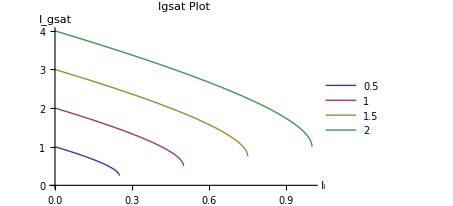

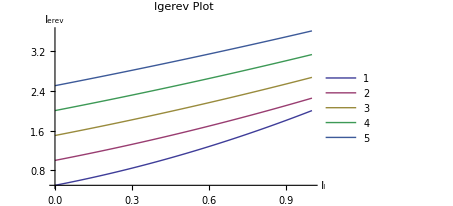

```mathematica
Igsat[pe_,pg_,Il_,Ie_,Ig_]:=pe/pg Ie-Il/pg+ √(pe/pg Ie(pe/pg Ie-2 Il/pg))
Ierev[pe_,pg_,Il_,Ie_,Ig_]:=1/pe Il+1/pe^2 Il^2 pe/(2pg)1/Ig+pg/(2pe)Ig
labelSize=13;
fieldSize=7;
titleLabelSize=14;
pe=1;
pg=1;
Plot[
{Igsat[pe,pg,Ileak,0.5,Ig],Igsat[pe,pg,Ileak,1,Ig],Igsat[pe,pg,Ileak,1.5,Ig],Igsat[pe,pg,Ileak,2,Ig]},
{Ileak, 0,1},
ImageSize->335,
PlotLabel->Style["Igsat Plot",titleLabelSize],
PlotLegends->{0.5,1,1.5,2},
AxesLabel->{Style["I_l",labelSize],Style["I_gsat",labelSize]}
]
Plot[
{Ierev[pe,pg,Ileak,Ie,1],Ierev[pe,pg,Ileak,Ie,2],Ierev[pe,pg,Ileak,Ie,3],Ierev[pe,pg,Ileak,Ie,4],Ierev[pe,pg,Ileak,Ie,5]},
{Ileak, 0,1},
ImageSize->335,
PlotLabel->Style["Igerev Plot",titleLabelSize],
PlotLegends->{1,2,3,4,5},
AxesLabel->{Style["I_l",labelSize],Style["I_erev",labelSize]}
]
```

### Automated Firing Rate Calculator Image Generator (for presentation)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{g→4.61334}

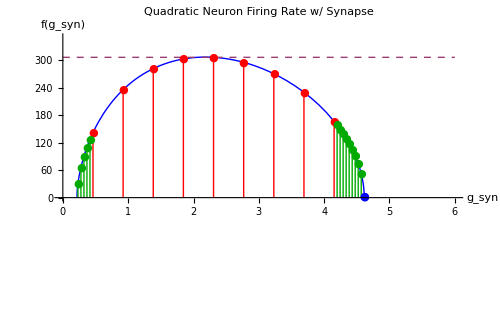

```mathematica
hsyn[vin_,gsyn_,erev_]:=(π+2 ArcTan[(1+gsyn)/(√(2 (vin+gsyn erev)-(1+gsyn)^2))])/(√(2 (vin+gsyn erev)-(1+gsyn)^2))
fsyn[vin_,gsyn_,erev_,τ_,tref_]:=1/(τ hsyn[vin,gsyn,erev]+tref)
Vin[Ic_,Il_,pqua_]:=pqua(Ic/Il)^2
Τ[Il_,ptau_]:=ptau/Il
Tref[Iref_,pref_]:=pref/Iref
Gsat[Igsat_,Il_,c1pgsat_]:=Igsat/(c1pgsat Il)
Erev[Ierev_,Il_,c1perev_]:=Ierev/(c1perev Il)
Gsyn[gsat_,trise_,ISI_]:=gsat trise/ISI 
Imprime[im_,vin_,τ_,gsyn_,erev_] :=(1/2 im^2-im + vin+gsyn(erev-im))/τ
ImprimeMin[vin_,τ_,gsyn_,erev_]:=(gsyn erev +vin-1/2(1+gsyn)^2)/τ
IgsatFn[c1pgsat_,c1perev_, Il_, Ierev_]:=c1pgsat/c1perev Ierev-c1pgsat Il+√(c1pgsat/c1perev Ierev(c1pgsat/c1perev Ierev-2 c1pgsat Il))
IerevFn[c1pgsat_,c1perev_,Il_,Igsat_]:=c1perev Il + 1/2 c1perev c1pgsat Il^2/Igsat+1/2 c1perev/c1pgsat Igsat
IgsatFn2[c1pgsat_,c2pgsat_, Il_]:=c2pgsat-c1pgsat Il+√(c2pgsat(c2pgsat-2 c1pgsat Il))
IerevFn2[c1perev_,c2perev_,Il_]:=c1perev Il + 1/2(c1perev Il)^2/c2perev+1/2 c2perev
Ic=0;Il=.45;Iref=2622.4075624201;Igsat=1.00; Ierev=.5;pqua=2.150182;ptau=0.000630;pref=0.0266169;c1pgsat=1.07908; c1perev=0.325357;c2pgsat=1.673024;c2perev=.287502;tsynrise=.175;ISIsyn=.175;vinMax=2; gsynMax = 6;fMax=350;vmMax=5; primeMax=100; ilMax=0.5;
gbif =Solve[fsyn[Vin[Ic,Il,pqua],g,Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]==0,g][[2]]
mainGsyns=Table[g i/10,{i,10}]/.gbif;
mainGsynTable =Table[{i,fsyn[Vin[Ic,Il,pqua],i,Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]},{i,mainGsyns}];
lowerMinorGsyns=Table[g i/100,{i,9}]/.gbif;
lowerMinorGsynTable =Table[{i,fsyn[Vin[Ic,Il,pqua],i,Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]},{i,lowerMinorGsyns}];
upperMinorGsyns=Table[g-(g i/100),{i,-10,9}]/.gbif;
upperMinorGsynTable =Table[{i,fsyn[Vin[Ic,Il,pqua],i,Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]},{i,upperMinorGsyns}];
Show[
Plot[{
fsyn[Vin[Ic,Il,pqua],gsynit,Erev[Ierev,Il,c1perev],Τ[Il,ptau],Tref[Iref,pref]],fsyn[Vin[Ic,Il,pqua],Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]
},
{gsynit,0,gsynMax},
PlotRange->{0,Max[fMax,fsyn[Vin[Ic,Il,pqua],gsynMax/2,Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]]},
PlotLabel->Style["Quadratic Neuron Firing Rate w/ Synapse",titleLabelSize],
AxesLabel->{Style["g_syn",labelSize],Style["f(g_syn)",labelSize]},
ImageSize->500,
PlotStyle->{Blue,Dashed}
],
ListPlot[
{
{g-.0001,fsyn[Vin[Ic,Il,pqua],g-.0001,Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]}/.gbif
},PlotStyle->Blue,PlotMarkers->{"●",Medium}
],
ListPlot[
{
(*{Table[fsyn[Vin[Ic,Il,pqua],i,Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]],{i,mainGsyns}]}*)
mainGsynTable
},PlotStyle->Red,PlotMarkers->{"●",Small}, Filling-> Axis, FillingStyle->Red,PlotRange->{0,350}
],
ListPlot[
{
(*{Table[fsyn[Vin[Ic,Il,pqua],i,Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]],{i,mainGsyns}]}*)
lowerMinorGsynTable,upperMinorGsynTable
},PlotStyle->Darker[Green],PlotMarkers->{"●"}, Filling-> Axis, FillingStyle->Darker[Green],PlotRange->{0,350}
]
]
```

### Difference between C1 and C2

3.415

2.2027

2.23302

0.469822

0.303039

0.307209

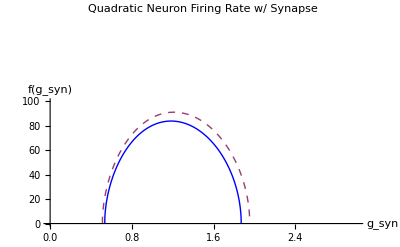

```mathematica
hsyn[vin_,gsyn_,erev_]:=(π+2 ArcTan[(1+gsyn)/(√(2 (vin+gsyn erev)-(1+gsyn)^2))])/(√(2 (vin+gsyn erev)-(1+gsyn)^2))
fsyn[vin_,gsyn_,erev_,τ_,tref_]:=1/(τ hsyn[vin,gsyn,erev]+tref)
Vin[Ic_,Il_,pqua_]:=pqua(Ic/Il)^2
Τ[Il_,ptau_]:=ptau/Il
Tref[Iref_,pref_]:=pref/Iref
Gsat[Igsat_,Il_,c1pgsat_]:=Igsat/(c1pgsat Il)
Erev[Ierev_,Il_,c1perev_]:=Ierev/(c1perev Il)
ierev[Erev_,Il_,c1perev_]:=Erev c1perev Il 
Gsyn[gsat_,trise_,ISI_]:=gsat trise/ISI 
Imprime[im_,vin_,τ_,gsyn_,erev_] :=(1/2 im^2-im + vin+gsyn(erev-im))/τ
ImprimeMin[vin_,τ_,gsyn_,erev_]:=(gsyn erev +vin-1/2(1+gsyn)^2)/τ
IgsatFn[c1pgsat_,c1perev_, Il_, Ierev_]:=c1pgsat/c1perev Ierev-c1pgsat Il+√(c1pgsat/c1perev Ierev(c1pgsat/c1perev Ierev-2 c1pgsat Il))
IerevFn[c1pgsat_,c1perev_,Il_,Igsat_]:=c1perev Il + 1/2 c1perev c1pgsat Il^2/Igsat+1/2 c1perev/c1pgsat Igsat
IgsatFn2[c1pgsat_,c2pgsat_, Il_]:=c2pgsat-c1pgsat Il+√(c2pgsat(c2pgsat-2 c1pgsat Il))
IerevFn2[c1perev_,c2perev_,Il_]:=c1perev Il + 1/2(c1perev Il)^2/c2perev+1/2 c2perev
Ic=0;Il=.43084133;Iref=2622.41;Igsat=1.00; Ierev=.469822;pqua=2.55922987;ptau=0.000603;pref=0.0279499;c1pgsat=1.187626; c1perev=0.319319;c2pgsat=1.906463;c2perev=0.257392;tsynrise=.175;ISIsyn=.175;vinMax=2; gsynMax = 3;fMax=100;vmMax=5; primeMax=100; ilMax=0.5;
gbif =Solve[fsyn[Vin[Ic,Il,pqua],g,Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]==0,g][[2]];
mainGsyns=Table[g i/10,{i,10}]/.gbif;
mainGsynTable =Table[{i,fsyn[Vin[Ic,Il,pqua],i,Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]},{i,mainGsyns}];
lowerMinorGsyns=Table[g i/100,{i,9}]/.gbif;
lowerMinorGsynTable =Table[{i,fsyn[Vin[Ic,Il,pqua],i,Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]},{i,lowerMinorGsyns}];
upperMinorGsyns=Table[g-(g i/100),{i,-10,9}]/.gbif;
upperMinorGsynTable =Table[{i,fsyn[Vin[Ic,Il,pqua],i,Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]},{i,upperMinorGsyns}];
Erev[Ierev,Il,c1perev]
Erev[IerevFn2[c1perev,c2perev,Il],Il,c1perev]
Erev[IerevFn[c1pgsat,c1perev,Il,Igsat],Il,c1perev]
Ierev
IerevFn2[c1perev,c2perev,Il]
IerevFn[c1pgsat,c1perev,Il,Igsat]

Show[
Plot[{
(*fsyn[Vin[Ic,Il,pqua],gsynit,Erev[Ierev,Il,c1perev],Τ[Il,ptau],Tref[Iref,pref]],*)
fsyn[Vin[Ic,Il,pqua],gsynit,Erev[IerevFn2[c1perev,c2perev,Il],Il,c1perev],Τ[Il,ptau],Tref[Iref,pref]],
fsyn[Vin[Ic,Il,pqua],gsynit,Erev[IerevFn[c1pgsat,c1perev,Il,Igsat],Il,c1perev],Τ[Il,ptau],Tref[Iref,pref]](*,
fsyn[Vin[Ic,Il,pqua],Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]*)
},{gsynit,0,gsynMax},
PlotRange->{0,Max[fMax,fsyn[Vin[Ic,Il,pqua],gsynMax/2,Erev[IerevFn[c1pgsat,c1perev,Il,Igsat],Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]]},
PlotLabel->Style["Quadratic Neuron Firing Rate w/ Synapse",titleLabelSize],
AxesLabel->{Style["g_syn",labelSize],Style["f(g_syn)",labelSize]},
ImageSize->400,
PlotStyle->{Blue,Dashed}],
ListPlot[{
{Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn], fsyn[Vin[Ic,Il,pqua],Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]}},
PlotStyle->Red,
PlotMarkers->{"●",Small}]
]
```

### Temperature Dependence Data (for Presentation)

(oldData_run1 | oldData_run1.1 | oldData_run1.2 | oldData_run1.3 | oldData_run1.4 | oldData_run1.5 | oldData_run1.7 | oldData_run1.8 | oldData_run1.9 | oldData_run2.0
0.882452 | 1.07908 | 1.15381 | 0.974237 | 1.07908 | 1.20379 | 1.18015 | 1.15381 | 1.15292 | 1.09176
0.333297 | 0.325357 | 0.321453 | 0.322581 | 0.32241 | 0.329057 | 0.321453 | 0.330221 | 0.319811 | 0.329354
1.37039 | 1.67302 | 1.81424 | 1.60642 | 1.67302 | 1.8244 | 1.84635 | 1.81424 | 1.90103 | 1.75254
0.360669 | 0.287502 | 0.264962 | 0.311781 | 0.2873 | 0.268991 | 0.264962 | 0.260137 | 0.246229 | 0.268691)

{0.882452,1.07908,1.15381,0.974237,1.07908,1.20379,1.18015,1.15381,1.15292,1.09176}

{0.333297,0.325357,0.321453,0.322581,0.32241,0.329057,0.321453,0.330221,0.319811,0.329354}

{1.37039,1.67302,1.81424,1.60642,1.67302,1.8244,1.84635,1.81424,1.90103,1.75254}

{0.360669,0.287502,0.264962,0.311781,0.2873,0.268991,0.264962,0.260137,0.246229,0.268691}

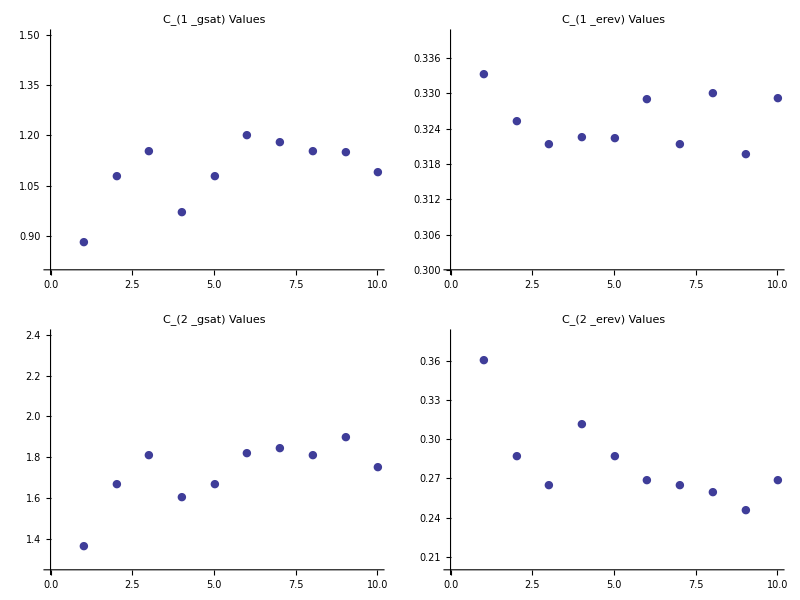

```mathematica
tempData ={
{"oldData_run1","oldData_run1.1","oldData_run1.2","oldData_run1.3","oldData_run1.4","oldData_run1.5","oldData_run1.7","oldData_run1.8","oldData_run1.9","oldData_run2.0"},
{0.8824520906036365,1.0790805339007432,1.1538052067906519,0.97423716045528785,1.0790805339007432,1.203793968285338,1.1801503579381925,1.1538052067906519,1.1529207139550586,1.0917621072469668},
{0.33329737683999283,0.32535718736928293,0.32145304015252851,0.32258126044913371,0.32241028854833853,0.32905720518592602,0.32145304015252851,0.33022081738686865,0.31981108400659286,0.32935371009183106},
{1.3703918102022727,1.6730241965367048,1.8142418106904821,1.6064248800229026,1.6730241965367048,1.8244010765828447,1.8463476419291869,1.8142418106904821,1.9010310361934664,1.752541083985854},
{0.36066900117976047,0.28750213331517543,0.26496221008700133,0.311781199871278,0.28729984505266243,0.26899093523701473,0.26496221008700133,0.26013723890795193,0.24622887664164267,0.26869145272954492}
}
c1Gsats=tempData[[2]]
c1Erevs=tempData[[3]]
c2Gsats=tempData[[4]]
c2Erevs=tempData[[5]]

(*AxesLabel->{Style["I_l",labelSize],Style["I_erev",labelSize]},*)

imageSize = 400;
titleLabelSize1 = 15;
Grid[{
{
ListPlot[c1Gsats,
PlotRange->{0.8,1.5},
PlotMarkers->{"●",Small},
PlotLabel->Style["C_(1  _gsat) Values",titleLabelSize1],
ImageSize->imageSize
],
ListPlot[c1Erevs,
PlotRange->{0.30,0.34},
PlotMarkers->{"●",Small},
PlotLabel->Style["C_(1  _erev) Values",titleLabelSize1],
ImageSize->imageSize
]
},
{
ListPlot[c2Gsats,
PlotRange->{1.25,2.4},
PlotMarkers->{"●",Small},
PlotLabel->Style["C_(2  _gsat) Values",titleLabelSize1],
ImageSize->imageSize
],
ListPlot[c2Erevs,
PlotRange->{0.2,0.38},
PlotMarkers->{"●",Small},
PlotLabel->Style["C_(2  _erev) Values",titleLabelSize1],
ImageSize->imageSize
]
}
}]
```

(oldData_run1 | oldData_run1.1 | oldData_run1.2 | oldData_run1.3 | oldData_run1.4 | oldData_run1.5 | oldData_run1.7 | oldData_run1.8 | oldData_run1.9 | oldData_run2.0
0.882452 | 1.07908 | 1.15381 | 0.974237 | 1.07908 | 1.20379 | 1.18015 | 1.15381 | 1.15292 | 1.09176
0.333297 | 0.325357 | 0.321453 | 0.322581 | 0.32241 | 0.329057 | 0.321453 | 0.330221 | 0.319811 | 0.329354
1.37039 | 1.67302 | 1.81424 | 1.60642 | 1.67302 | 1.8244 | 1.84635 | 1.81424 | 1.90103 | 1.75254
0.360669 | 0.287502 | 0.264962 | 0.311781 | 0.2873 | 0.268991 | 0.264962 | 0.260137 | 0.246229 | 0.268691)

{0.882452,1.07908,1.15381,0.974237,1.07908,1.20379,1.18015,1.15381,1.15292,1.09176}

{0.333297,0.325357,0.321453,0.322581,0.32241,0.329057,0.321453,0.330221,0.319811,0.329354}

{1.37039,1.67302,1.81424,1.60642,1.67302,1.8244,1.84635,1.81424,1.90103,1.75254}

{0.360669,0.287502,0.264962,0.311781,0.2873,0.268991,0.264962,0.260137,0.246229,0.268691}

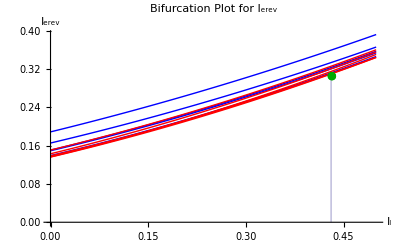

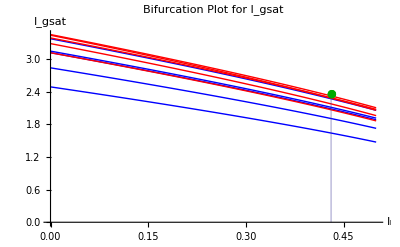

```mathematica
fsyn[vin_,gsyn_,erev_,τ_,tref_]:=1/(τ hsyn[vin,gsyn,erev]+tref)
Vin[Ic_,Il_,pqua_]:=pqua(Ic/Il)^2
Τ[Il_,ptau_]:=ptau/Il
Tref[Iref_,pref_]:=pref/Iref
Gsat[Igsat_,Il_,c1pgsat_]:=Igsat/(c1pgsat Il)
Erev[Ierev_,Il_,c1perev_]:=Ierev/(c1perev Il)
ierev[Erev_,Il_,c1perev_]:=Erev c1perev Il 
Gsyn[gsat_,trise_,ISI_]:=gsat trise/ISI 
Imprime[im_,vin_,τ_,gsyn_,erev_] :=(1/2 im^2-im + vin+gsyn(erev-im))/τ
ImprimeMin[vin_,τ_,gsyn_,erev_]:=(gsyn erev +vin-1/2(1+gsyn)^2)/τ
IgsatFn[c1pgsat_,c1perev_, Il_, Ierev_]:=c1pgsat/c1perev Ierev-c1pgsat Il+√(c1pgsat/c1perev Ierev(c1pgsat/c1perev Ierev-2 c1pgsat Il))
IerevFn[c1pgsat_,c1perev_,Il_,Igsat_]:=c1perev Il + 1/2 c1perev c1pgsat Il^2/Igsat+1/2 c1perev/c1pgsat Igsat
IgsatFn2[c1pgsat_,c2pgsat_, Il_]:=c2pgsat-c1pgsat Il+√(c2pgsat(c2pgsat-2 c1pgsat Il))
IerevFn2[c1perev_,c2perev_,Il_]:=c1perev Il + 1/2(c1perev Il)^2/c2perev+1/2 c2perev
tempData ={
{"oldData_run1","oldData_run1.1","oldData_run1.2","oldData_run1.3","oldData_run1.4","oldData_run1.5","oldData_run1.7","oldData_run1.8","oldData_run1.9","oldData_run2.0"},
{0.8824520906036365,1.0790805339007432,1.1538052067906519,0.97423716045528785,1.0790805339007432,1.203793968285338,1.1801503579381925,1.1538052067906519,1.1529207139550586,1.0917621072469668},
{0.33329737683999283,0.32535718736928293,0.32145304015252851,0.32258126044913371,0.32241028854833853,0.32905720518592602,0.32145304015252851,0.33022081738686865,0.31981108400659286,0.32935371009183106},
{1.3703918102022727,1.6730241965367048,1.8142418106904821,1.6064248800229026,1.6730241965367048,1.8244010765828447,1.8463476419291869,1.8142418106904821,1.9010310361934664,1.752541083985854},
{0.36066900117976047,0.28750213331517543,0.26496221008700133,0.311781199871278,0.28729984505266243,0.26899093523701473,0.26496221008700133,0.26013723890795193,0.24622887664164267,0.26869145272954492}
}
c1Gsats=tempData[[2]]
c1Erevs=tempData[[3]]
c2Gsats=tempData[[4]]
c2Erevs=tempData[[5]]

Ic=0;Il=.43084133;Iref=2622.41;Igsat=1.00; Ierev=.469822;pqua=2.55922987;ptau=0.000603;pref=0.0279499;
c1pgsat0=0.882452; c1perev0=0.333297;
(*c1pgsat=1.187626; c1perev=0.319319;*)
c1pgsat1=1.180150; c1perev1=0.321453;
c2pgsat=1.906463;c2perev=0.257392;tsynrise=.175;ISIsyn=.175;vinMax=2; gsynMax = 3;fMax=100;vmMax=5; primeMax=100; ilMax=0.5;
Show[
Plot[{
IerevFn[c1Gsats[[1;;5]],c1Erevs[[1;;5]], Ilk, Igsat],
IerevFn[c1Gsats[[6;;10]],c1Erevs[[6;;10]], Ilk, Igsat]
(*IerevFn[c1pgsat0,c1perev0, Ilk, Igsat],
IerevFn[c1Gsats[[{1,7}]],c1Erevs[[{1,7}]], Ilk, Igsat],
IerevFn[c1pgsat1,c1perev1, Ilk, Igsat]*)
},
{Ilk,0,ilMax},
PlotLabel->Style["Bifurcation Plot for I_erev",titleLabelSize],
AxesLabel->{Style["I_l",labelSize],Style["I_erev",labelSize]},
PlotStyle->{Blue,Red,Green},
PlotRange->{0,All},
ImageSize->400(*,
Filling->{1-> Top}*)
],
ListPlot[{
{Il, IerevFn[c1pgsat,c1perev,Il,Igsat]}
},
PlotStyle->Darker[Green],
PlotMarkers->{"●",Small},
Filling->Axis
]
]
Show[
Plot[{
IgsatFn[c1Gsats[[1;;5]],c1Erevs[[1;;5]], Ilk, Ierev],
IgsatFn[c1Gsats[[6;;10]],c1Erevs[[6;;10]], Ilk, Ierev]
(*IgsatFn[c1pgsat0,c1perev0, Ilk, Ierev],
IgsatFn[c1pgsat1,c1perev1, Ilk, Ierev]*)
},
{Ilk,0,ilMax},
ImageSize->400,
PlotRange->{0,All},
PlotStyle->{Blue,Red},
PlotLabel->Style["Bifurcation Plot for I_gsat",titleLabelSize],
AxesLabel->{Style["I_l",labelSize],Style["I_gsat",labelSize]}(*,
Filling->{1-> Axis}*)
],
ListPlot[{
{Il, IgsatFn[c1pgsat,c1perev,Il,Ierev]}
},
PlotStyle->Darker[Green],
PlotMarkers->{"●",Small},
Filling-> Axis
]
]
(*Show[
Plot[{
(*fsyn[Vin[Ic,Il,pqua],gsynit,Erev[Ierev,Il,c1perev],Τ[Il,ptau],Tref[Iref,pref]],*)
fsyn[Vin[Ic,Il,pqua],gsynit,Erev[IerevFn2[c1perev,c2perev,Il],Il,c1perev],Τ[Il,ptau],Tref[Iref,pref]],
fsyn[Vin[Ic,Il,pqua],gsynit,Erev[IerevFn[c1pgsat,c1perev,Il,Igsat],Il,c1perev],Τ[Il,ptau],Tref[Iref,pref]](*,
fsyn[Vin[Ic,Il,pqua],Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]*)
},{gsynit,0,gsynMax},
PlotRange->{0,Max[fMax,fsyn[Vin[Ic,Il,pqua],gsynMax/2,Erev[IerevFn[c1pgsat,c1perev,Il,Igsat],Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]]},
PlotLabel->Style["Quadratic Neuron Firing Rate w/ Synapse",titleLabelSize],
AxesLabel->{Style["g_syn",labelSize],Style["f(g_syn)",labelSize]},
ImageSize->400,
PlotStyle->{Blue,Dashed}],
ListPlot[{
{Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn], fsyn[Vin[Ic,Il,pqua],Gsyn[Gsat[Igsat,Il,c1pgsat],tsynrise,ISIsyn],Erev[Ierev,Il,c1perev] ,Τ[Il,ptau],Tref[Iref,pref]]}},
PlotStyle->Red,
PlotMarkers->{"●",Small}]
]*)
```

### Solving LPF Equations

#### LPF Equations and Manipulator

```mathematica
imgSize=380;
expPower=-15;
spacerWidth=40;
expDecay[t_,τ_,isat_]:=(isat*10^expPower) ⅇ^(-t/τ);
expDecayOffset[t_,τ_,isat_,offset_]:=(isat*10^expPower )ⅇ^(-t/τ) +(offset*10^expPower);
diffExpDecayLog[t_,τ_,isat_]:=D[Log[expDecay[t,τ,isat]],t];
Grid[{{Text["Basic"],Spacer[spacerWidth],Text["w/ Offset"]},{Text["I_m=I_satⅇ^(-FractionBox[t, τ])"],Spacer[spacerWidth],Text["I_m=I_satⅇ^(-FractionBox[t, τ])+I_offset"]},{Text["I_m/I_sat=ⅇ^(-FractionBox[t, τ])"],Spacer[spacerWidth],Text["I_m/I_sat=ⅇ^(-FractionBox[t, τ])"]},{Text["ln(I_m/I_sat)=-t/τ"],Spacer[spacerWidth],Text["ln(I_m/I_sat)=-t/τ"]},{Text["d/dt(ln(I_m/I_sat))=-1/τ"],Spacer[spacerWidth],Text["d/dt(ln(I_m/I_sat))=-1/τ"]},{Text["τ=-1/(d/dt)"],Spacer[spacerWidth],Text["τ=-1/(d/dt)"]}}]
Manipulate[
Grid[{{
Plot[{expDecay[t,τ,isat],expDecayOffset[t,τ,isat,offset],isat*10^expPower,(isat*10^expPower)/ⅇ,(isat+offset)*10^expPower,(isat*10^expPower)/ⅇ+offset*10^expPower},{t,0,tmax},PlotRange->{{0,tmax},{0,Immax}},ImageSize->imgSize,PlotLabel->"Exponential Curves",AxesLabel->{"t(s)","I_m(A)"}],
LogPlot[{expDecay[t,τ,isat],expDecayOffset[t,τ,isat,offset]},{t,0,tmax},PlotRange->{{0,tmax},{Immin,Immax}},ImageSize-> imgSize,PlotLabel->"Log Exponential Curves",AxesLabel->{"t(s)","Log(I_m) (A)"}],
Plot[{-1/diffExpDecayLog[t,τ,isat],t1/τ},{t1,0,tmax},PlotRange-> {{0,tmax},{0,τmax}},ImageSize->imgSize,PlotLabel->"Tau Values",AxesLabel->{"t(s)","τ(s)"}]
}}],
Style["Parameter Control",Bold],
Row[{Control[{{τ,.01,"τ(s)"},0.001,1,0.001, Appearance->{"Labeled","Open"}}],Control[{{isat,100,"i_sat(fA)"},10,1000,10, Appearance->{"Labeled","Open"}}],Control[{{offset,10,"offset(fA)"},0,100,1, Appearance->{"Labeled","Open"}}]},Spacer[20]],
Style["Axes Control", Bold],
{{tmax,.1,"t_max(s)"},.01,1,.01, Appearance->"Labeled"},
{{τmax,.1,"τ_max(s)"},τ,1,.01, Appearance->"Labeled"},
{{Immin,10^(expPower-3),"Im_min(A)"},100*10^(expPower-6),Immax,10^expPower, Appearance->"Labeled"},
{{Immax,1.3*isat*10^expPower,"Im_max(A)"},Immin,10*10^-9,10^expPower, Appearance->"Labeled"},
ControlPlacement->{Top,Top,Top,Top,Top,Bottom,Bottom,Bottom,Bottom,Bottom},
Alignment->Left,
LabelStyle->Medium,
FrameLabel->{"","",Style["Low-Pass Filter Manipulator",Bold,Large]}
](*Manipulate*)
```

Basic |  | w/ Offset
I_m=I_satⅇ^(-FractionBox[t, τ]) |  | I_m=I_satⅇ^(-FractionBox[t, τ])+I_offset
I_m/I_sat=ⅇ^(-FractionBox[t, τ]) |  | I_m/I_sat=ⅇ^(-FractionBox[t, τ])
ln(I_m/I_sat)=-t/τ |  | ln(I_m/I_sat)=-t/τ
d/dt(ln(I_m/I_sat))=-1/τ |  | d/dt(ln(I_m/I_sat))=-1/τ
τ=-1/(d/dt) |  | τ=-1/(d/dt)

#### Derivation of LPF Equations

```mathematica
Row[{Simplify[DSolve[{y'[t]==-y[t]+d, y[0]==0,y[∞]==d},y[t],t]]⟦1⟧⟦1⟧,Text["Charging LPF"]},": "]
Row[{Simplify[DSolve[{y'[t]==-y[t], y[0]==d,y[∞]==0},y[t],t]]⟦1⟧⟦1⟧,Text["Discharging LPF"]},"            : "]
```

: : y(t)→d-d ⅇ^-tCharging LPF

:             : y(t)→d ⅇ^-tDischarging LPF

```mathematica
expDecay1[t_,τ_,isat_]:=(isat )ⅇ^(-t/τ) ;
Log[expDecay1[t,τ,isat]]
D[Log[expDecay1[t,τ,isat]],t]
```

log(isat ⅇ^(-t/τ))

-1/τ

```mathematica
expDecayOffset1[t_,τ_,isat_,offset_]:=(isat )ⅇ^(-t/τ) +offset;
Log[expDecayOffset1[t,τ,isat,offset]-offset]
D[Log[expDecayOffset1[t,τ,isat,offset]-offset],t]
```

log(isat ⅇ^(-t/τ))

-1/τ

```mathematica
ControllerInformation[]
```

```mathematica
Dynamic[ControllerState["Axes"]]
```